```mathematica
(* INTENSITY PLOT OF FROZEN WAVES *)
```

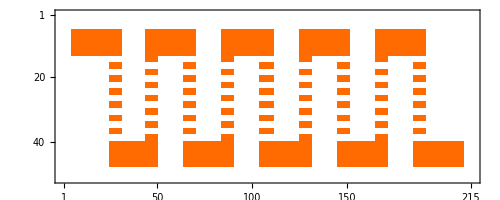

```mathematica
(* F profile *)
myImage=-Graphics-;
myImageData=Reverse[1-ImageData[Binarize[myImage]]];
pxX=Dimensions[myImageData][[1]];(* Height in pixels (x axis) *)
pxZ=Dimensions[myImageData][[2]];(* Length in pixels (z axis) *)
fileIntensityProfile = NotebookDirectory[]<>"function-f.mtx";
Export[fileIntensityProfile,myImageData,"MTX"];
MatrixPlot[Reverse[myImageData]]
```

```mathematica
(* Fields *)
field=Import[NotebookDirectory[]<>"field.wl"];

(* Intensity *)
fieldIntensity=Transpose[Abs[field]^2,2<->1][[1]];
intMax=SetPrecision[Round[Max[fieldIntensity],0.01],3];
intTicks={0,0.2,0.4,0.6,0.8,1.0,1.2,1.4};

(* x *)
xmin=0;
xmax=1.17;
xticks={0,1.17};
xaxis="x (cm)";
(* z *)
zmin=0;
zmax=10;
zticks={0,2,4,6,8,10};
zaxis="z (cm)";

(* Schemes *)
myBackColor = White;
myForeColor = Gray;
myFontColor=Black;
myColorData={"AvocadoColors",{0,intMax}};
myLabelStyle = {FontFamily->"Arial",FontSize->11,FontWeight->"Plain",FontColor-> myFontColor};
myImageResolution=150;

(* Plots *)
Export[NotebookDirectory[]<>"plot1.png",
MatrixPlot[myImageData,AspectRatio->pxX/pxZ,PlotLabel->"F(x,z)",FrameLabel->{"x (px)","z (px)"},FrameTicks-> {{{1,25,51},None},{{1,43,86,129,172,215},None}},LabelStyle->myLabelStyle,DataReversed->{True,False}],ImageResolution->myImageResolution];


Export[NotebookDirectory[]<>"plot2.png",
ListDensityPlot[fieldIntensity,PlotRange->{0,intMax},DataRange->{{zmin,zmax},{xmin,xmax}},FrameTicks-> {{xticks,None},{zticks,None}},Frame-> True, PlotLabel->"|ψ_LSLS|^2",FrameLabel->{zaxis,xaxis},LabelStyle->myLabelStyle,ColorFunction->ColorData[myColorData],ColorFunctionScaling->True,PlotLegends->BarLegend[myColorData,Ticks->intTicks,LegendMarkerSize->190],AspectRatio->pxX/pxZ],ImageResolution->myImageResolution];

Export[NotebookDirectory[]<>"plot3.png",
ListPlot3D[fieldIntensity,PlotRange->{0,intMax},DataRange->{{zmin,zmax},{xmin,xmax}},Ticks->{zticks,xticks,{0,intMax}},AxesLabel->{zaxis,xaxis},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},PlotLabel->"|ψ_LSLS|^2",LabelStyle->myLabelStyle,ColorFunction->ColorData[myColorData],BoxRatios->{pxZ,pxX,1.5pxX},ViewPoint->{1.3,-3.4,3.5}],ImageResolution->myImageResolution];
```